## CSE 477 / G.Farin B-spline Least Squares

Data points are data[[1]] thru data[[m+1]], associated parameter values are in tt[[1]] thru tt[[m+1]] where m>> n, n being the degree of the approximating B-spline curve.

  The B-splines are defined over a knot sequence knot[[1]] thru knot[[2n+ll+1]] where ll is the number of domain intervals.

The coefficient matrix vandermonde has m+1 rows (a lot) and   n+ll colums.
Solution: control points dd[[1]] thru dd[[n+ll]].

```mathematica
(SetDirectory[ToFileName[Extract["FileName"/.NotebookInformation[EvaluationNotebook[]],{1},FrontEnd`FileName]]];)
```

```mathematica
approx[n_,knot_,data_,tt_]:=
(m=Length[data]-1;
ll=Length[knot]-2*n-1; (* domain intervals *)

(* van is the Vandermonde matrix which typically has (many) more roes than columns *)
van=Table[BSplineBasis[{n,knot},j,tt[[i]]],{i,1,m+1},{j,0,n+ll-1 }];
dd=LinearSolve[Transpose[van].van,Transpose[van].data];
dataplot=ListPlot[data,PlotStyle-> Thick];
points=Graphics[{Red,PointSize[0.015],Point[dd]}];
ddplot=ListLinePlot[dd];
curve[t_]:=Sum[BSplineBasis[{n,knot},i,t]*dd[[i+1]],{i,0,n+ll-1}];
cplot=ParametricPlot[curve[t],{t,knot[[1]],knot[[2n+ll+1]]},PlotStyle->{Thick,Green}];
approxpic=Show[{ddplot,cplot, points,dataplot},Axes-> False]
);
```

SetDelayed::write: Tag Graphics in (GraphicsBox[List[List[List[], List[], List[Hue[0.67`, 0.6`, 0.6`], Thickness[Large], LineBox[List[List[0.8`, 1.2000000000000002`], List[0.8086336213955122`, 1.2128582499964404`], List[0.8173594248878522`, 1.2256704089444668`], List[0.835087578163016`, 1.2511564536952775`], List[0.8716500698752786`, 1.3015754506159314`], List[0.9491997939475434`, 1.400201074133369`], List[0.959308328892302`, 1.412321867355186`], List[0.9695090459338888`, 1.424396569528589`], List[0.9901870263075456`, 1.448407700730153`], List[1.0326491722167948`, 1.4958768705523136`], List[1.1219982046830315`, 1.5886028398727634`], List[1.1335816531770355`, 1.599986176319956`], List[1.1452572837678687`, 1.6113234217187355`], List[1.168885091240019`, 1.6338596393710532`], List[1.2172468913462544`, 1.6783789820947206`], List[1.3183952322064654`, 1.7652052972181855`], List[1.3314535942497172`, 1.7758511768907554`], List[1.3446041383897973`, 1.7864509655149117`], List[1.3711817729604405`, 1.8075122696179826`], List[1.4254432272636626`, 1.849081785243157`], List[1.5383908765178465`, 1.9300084461696352`], List[1.554150815677506`, 1.9407482104882419`], List[1.5700190968654317`, 1.9514338037927168`], List[1.602080685326078`, 1.9726424773592683`], List[1.6675039665865528`, 2.0144097723227805`], List[1.8035509464642294`, 2.095344153571438`], List[1.8210443580761335`, 2.1052171816639245`], List[1.8386461117163013`, 2.1150360387422773`], List[1.8741746450814318`, 2.1345112398565846`], List[1.946531816150879`, 2.172811589915611`], List[2.0964465756465014`, 2.2468120813552974`], List[2.115673459710647`, 2.2558183732216612`], List[2.1350086858030592`, 2.2647704940738933`], List[2.174004164072678`, 2.2825122227359587`], List[2.2532952249510974`, 2.3173456278904982`], List[2.417077764064665`, 2.384412229521213`], List[2.438038120581053`, 2.3925517851614546`], List[2.4591068191257084`, 2.400637169787565`], List[2.501569242299813`, 2.416645425997388`], List[2.587794192987204`, 2.448011886247441`], List[2.7654445117187145`, 2.5081445980691823`], List[2.7866311071541126`, 2.5149371360255905`], List[2.8079121611151607`, 2.5216824447191715`], List[2.850757644614218`, 2.5350313743178563`], List[2.9375821139201586`, 2.561162482361313`], List[3.115765061763346`, 2.6111576938325736`], List[3.1384629936091795`, 2.6171945635837637`], List[3.161255383980665`, 2.623184204072128`], List[3.207123540300593`, 2.6350217972603773`], List[3.2999933552482745`, 2.658130232482964`], Skeleton[626]]]]]], List[Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[Method, List[]], Rule[PlotRange, List[List[0.`, 24.998151151716584`], List[0.`, 24.99999066325131`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Scaled[0.02`], Scaled[0.02`]]]]]) is Protected.

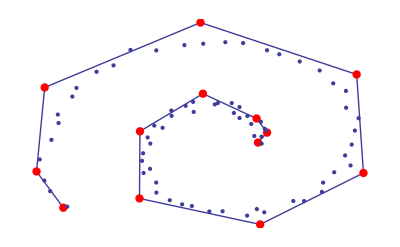

```mathematica
n=3;  (* degree *)
m=70; (* counting from 0 to m *)
ll=10;  (* domain intervals *)
tt1=Table[t,{t,0.0,1.0,1/m}]; (* data point parameter values *)

knot=Join[Table[0,{i,0,n}],Table[i/ll,{i,1,ll-1}],Table[1,{i,0,n}]]//N;

data1=Table[{(2+t)Cos[t]+ RandomReal[], (2+t)Sin[t]+ RandomReal[]},{t,0,10.0,10/m}]//N;

approx[n,knot,data1,tt1]
(*Export["spiral-approx-cubic.eps",%]*)
```

We now use many more intervals (ll). The curve follows the data better, but it’s not a good curve anymore.

SetDelayed::write: Tag Graphics in (GraphicsBox[List[List[List[], List[], List[Hue[0.67`, 0.6`, 0.6`], Thickness[Large], LineBox[List[List[0.8`, 1.2000000000000002`], List[0.8086336213955122`, 1.2128582499964404`], List[0.8173594248878522`, 1.2256704089444668`], List[0.835087578163016`, 1.2511564536952775`], List[0.8716500698752786`, 1.3015754506159314`], List[0.9491997939475434`, 1.400201074133369`], List[0.959308328892302`, 1.412321867355186`], List[0.9695090459338888`, 1.424396569528589`], List[0.9901870263075456`, 1.448407700730153`], List[1.0326491722167948`, 1.4958768705523136`], List[1.1219982046830315`, 1.5886028398727634`], List[1.1335816531770355`, 1.599986176319956`], List[1.1452572837678687`, 1.6113234217187355`], List[1.168885091240019`, 1.6338596393710532`], List[1.2172468913462544`, 1.6783789820947206`], List[1.3183952322064654`, 1.7652052972181855`], List[1.3314535942497172`, 1.7758511768907554`], List[1.3446041383897973`, 1.7864509655149117`], List[1.3711817729604405`, 1.8075122696179826`], List[1.4254432272636626`, 1.849081785243157`], List[1.5383908765178465`, 1.9300084461696352`], List[1.554150815677506`, 1.9407482104882419`], List[1.5700190968654317`, 1.9514338037927168`], List[1.602080685326078`, 1.9726424773592683`], List[1.6675039665865528`, 2.0144097723227805`], List[1.8035509464642294`, 2.095344153571438`], List[1.8210443580761335`, 2.1052171816639245`], List[1.8386461117163013`, 2.1150360387422773`], List[1.8741746450814318`, 2.1345112398565846`], List[1.946531816150879`, 2.172811589915611`], List[2.0964465756465014`, 2.2468120813552974`], List[2.115673459710647`, 2.2558183732216612`], List[2.1350086858030592`, 2.2647704940738933`], List[2.174004164072678`, 2.2825122227359587`], List[2.2532952249510974`, 2.3173456278904982`], List[2.417077764064665`, 2.384412229521213`], List[2.438038120581053`, 2.3925517851614546`], List[2.4591068191257084`, 2.400637169787565`], List[2.501569242299813`, 2.416645425997388`], List[2.587794192987204`, 2.448011886247441`], List[2.7654445117187145`, 2.5081445980691823`], List[2.7866311071541126`, 2.5149371360255905`], List[2.8079121611151607`, 2.5216824447191715`], List[2.850757644614218`, 2.5350313743178563`], List[2.9375821139201586`, 2.561162482361313`], List[3.115765061763346`, 2.6111576938325736`], List[3.1384629936091795`, 2.6171945635837637`], List[3.161255383980665`, 2.623184204072128`], List[3.207123540300593`, 2.6350217972603773`], List[3.2999933552482745`, 2.658130232482964`], Skeleton[626]]]]]], List[Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[Method, List[]], Rule[PlotRange, List[List[0.`, 24.998151151716584`], List[0.`, 24.99999066325131`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Scaled[0.02`], Scaled[0.02`]]]]]) is Protected.

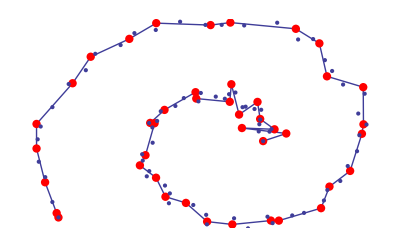

```mathematica
n=3;  (* degree *)
m=70; (* counting from 0 to m *)
ll=40;  (* domain intervals *)
tt1=Table[t,{t,0.0,1.0,1/m}]; (* data point parameter values *)

knot=Join[Table[0,{i,0,n}],Table[i/ll,{i,1,ll-1}],Table[1,{i,0,n}]]//N;

(*Increased noise level in data: *)
data1=Table[{(2+t)Cos[t]+ RandomReal[], (2+t)Sin[t]+ RandomReal[]},{t,0,10.0,10/m}]//N;

approx[n,knot,data1,tt1]
```

We now use a higher degree (n). The curve follows the data well, but it’s not a good curve either.

SetDelayed::write: Tag Graphics in (GraphicsBox[List[List[List[], List[], List[Hue[0.67`, 0.6`, 0.6`], Thickness[Large], LineBox[List[List[0.8`, 1.2000000000000002`], List[0.8086336213955122`, 1.2128582499964404`], List[0.8173594248878522`, 1.2256704089444668`], List[0.835087578163016`, 1.2511564536952775`], List[0.8716500698752786`, 1.3015754506159314`], List[0.9491997939475434`, 1.400201074133369`], List[0.959308328892302`, 1.412321867355186`], List[0.9695090459338888`, 1.424396569528589`], List[0.9901870263075456`, 1.448407700730153`], List[1.0326491722167948`, 1.4958768705523136`], List[1.1219982046830315`, 1.5886028398727634`], List[1.1335816531770355`, 1.599986176319956`], List[1.1452572837678687`, 1.6113234217187355`], List[1.168885091240019`, 1.6338596393710532`], List[1.2172468913462544`, 1.6783789820947206`], List[1.3183952322064654`, 1.7652052972181855`], List[1.3314535942497172`, 1.7758511768907554`], List[1.3446041383897973`, 1.7864509655149117`], List[1.3711817729604405`, 1.8075122696179826`], List[1.4254432272636626`, 1.849081785243157`], List[1.5383908765178465`, 1.9300084461696352`], List[1.554150815677506`, 1.9407482104882419`], List[1.5700190968654317`, 1.9514338037927168`], List[1.602080685326078`, 1.9726424773592683`], List[1.6675039665865528`, 2.0144097723227805`], List[1.8035509464642294`, 2.095344153571438`], List[1.8210443580761335`, 2.1052171816639245`], List[1.8386461117163013`, 2.1150360387422773`], List[1.8741746450814318`, 2.1345112398565846`], List[1.946531816150879`, 2.172811589915611`], List[2.0964465756465014`, 2.2468120813552974`], List[2.115673459710647`, 2.2558183732216612`], List[2.1350086858030592`, 2.2647704940738933`], List[2.174004164072678`, 2.2825122227359587`], List[2.2532952249510974`, 2.3173456278904982`], List[2.417077764064665`, 2.384412229521213`], List[2.438038120581053`, 2.3925517851614546`], List[2.4591068191257084`, 2.400637169787565`], List[2.501569242299813`, 2.416645425997388`], List[2.587794192987204`, 2.448011886247441`], List[2.7654445117187145`, 2.5081445980691823`], List[2.7866311071541126`, 2.5149371360255905`], List[2.8079121611151607`, 2.5216824447191715`], List[2.850757644614218`, 2.5350313743178563`], List[2.9375821139201586`, 2.561162482361313`], List[3.115765061763346`, 2.6111576938325736`], List[3.1384629936091795`, 2.6171945635837637`], List[3.161255383980665`, 2.623184204072128`], List[3.207123540300593`, 2.6350217972603773`], List[3.2999933552482745`, 2.658130232482964`], Skeleton[626]]]]]], List[Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[Method, List[]], Rule[PlotRange, List[List[0.`, 24.998151151716584`], List[0.`, 24.99999066325131`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Scaled[0.02`], Scaled[0.02`]]]]]) is Protected.

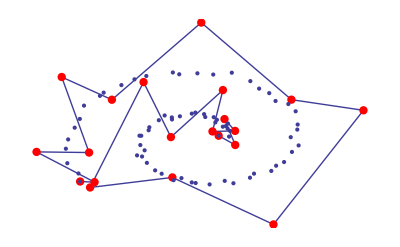

```mathematica
n=10;  (* degree *)
m=70; (* counting from 0 to m *)
ll=10;  (* domain intervals *)
tt1=Table[t,{t,0.0,1.0,1/m}]; (* data point parameter values *)

knot=Join[Table[0,{i,0,n}],Table[i/ll,{i,1,ll-1}],Table[1,{i,0,n}]]//N;

(*Increased noise level in data: *)
data1=Table[{(2+t)Cos[t]+ RandomReal[], (2+t)Sin[t]+ RandomReal[]},{t,0,10.0,10/m}]//N;
approx[n,knot,data1,tt1]
```

Next, we use only one domain interval. We get polynomial approximation (i.e., a Bezier curve),

SetDelayed::write: Tag Graphics in (GraphicsBox[List[List[List[], List[], List[Hue[0.67`, 0.6`, 0.6`], Thickness[Large], LineBox[List[List[0.8`, 1.2000000000000002`], List[0.8086336213955122`, 1.2128582499964404`], List[0.8173594248878522`, 1.2256704089444668`], List[0.835087578163016`, 1.2511564536952775`], List[0.8716500698752786`, 1.3015754506159314`], List[0.9491997939475434`, 1.400201074133369`], List[0.959308328892302`, 1.412321867355186`], List[0.9695090459338888`, 1.424396569528589`], List[0.9901870263075456`, 1.448407700730153`], List[1.0326491722167948`, 1.4958768705523136`], List[1.1219982046830315`, 1.5886028398727634`], List[1.1335816531770355`, 1.599986176319956`], List[1.1452572837678687`, 1.6113234217187355`], List[1.168885091240019`, 1.6338596393710532`], List[1.2172468913462544`, 1.6783789820947206`], List[1.3183952322064654`, 1.7652052972181855`], List[1.3314535942497172`, 1.7758511768907554`], List[1.3446041383897973`, 1.7864509655149117`], List[1.3711817729604405`, 1.8075122696179826`], List[1.4254432272636626`, 1.849081785243157`], List[1.5383908765178465`, 1.9300084461696352`], List[1.554150815677506`, 1.9407482104882419`], List[1.5700190968654317`, 1.9514338037927168`], List[1.602080685326078`, 1.9726424773592683`], List[1.6675039665865528`, 2.0144097723227805`], List[1.8035509464642294`, 2.095344153571438`], List[1.8210443580761335`, 2.1052171816639245`], List[1.8386461117163013`, 2.1150360387422773`], List[1.8741746450814318`, 2.1345112398565846`], List[1.946531816150879`, 2.172811589915611`], List[2.0964465756465014`, 2.2468120813552974`], List[2.115673459710647`, 2.2558183732216612`], List[2.1350086858030592`, 2.2647704940738933`], List[2.174004164072678`, 2.2825122227359587`], List[2.2532952249510974`, 2.3173456278904982`], List[2.417077764064665`, 2.384412229521213`], List[2.438038120581053`, 2.3925517851614546`], List[2.4591068191257084`, 2.400637169787565`], List[2.501569242299813`, 2.416645425997388`], List[2.587794192987204`, 2.448011886247441`], List[2.7654445117187145`, 2.5081445980691823`], List[2.7866311071541126`, 2.5149371360255905`], List[2.8079121611151607`, 2.5216824447191715`], List[2.850757644614218`, 2.5350313743178563`], List[2.9375821139201586`, 2.561162482361313`], List[3.115765061763346`, 2.6111576938325736`], List[3.1384629936091795`, 2.6171945635837637`], List[3.161255383980665`, 2.623184204072128`], List[3.207123540300593`, 2.6350217972603773`], List[3.2999933552482745`, 2.658130232482964`], Skeleton[626]]]]]], List[Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[Method, List[]], Rule[PlotRange, List[List[0.`, 24.998151151716584`], List[0.`, 24.99999066325131`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Scaled[0.02`], Scaled[0.02`]]]]]) is Protected.

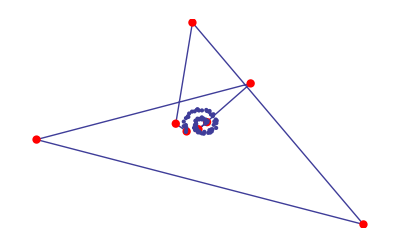

```mathematica
n=7;  (* degree *)
m=70; (* counting from 0 to m *)
ll=1;  (* domain intervals *)
tt1=Table[t,{t,0.0,1.0,1/m}]; (* data point parameter values *)

knot=Join[Table[0,{i,0,n}],Table[i/ll,{i,1,ll-1}],Table[1,{i,0,n}]]//N;

data1=Table[{(2+t)Cos[t]+ 2RandomReal[], (2+t)Sin[t]+ 2RandomReal[]},{t,0,10.0,10/m}]//N;

approx[n,knot,data1,tt1]
```

Next, we again use only one domain interval, and the number of data points equals the number of unknowns. We get polynomial interpolation.

SetDelayed::write: Tag Graphics in (GraphicsBox[List[List[List[], List[], List[Hue[0.67`, 0.6`, 0.6`], Thickness[Large], LineBox[List[List[0.8`, 1.2000000000000002`], List[0.8086336213955122`, 1.2128582499964404`], List[0.8173594248878522`, 1.2256704089444668`], List[0.835087578163016`, 1.2511564536952775`], List[0.8716500698752786`, 1.3015754506159314`], List[0.9491997939475434`, 1.400201074133369`], List[0.959308328892302`, 1.412321867355186`], List[0.9695090459338888`, 1.424396569528589`], List[0.9901870263075456`, 1.448407700730153`], List[1.0326491722167948`, 1.4958768705523136`], List[1.1219982046830315`, 1.5886028398727634`], List[1.1335816531770355`, 1.599986176319956`], List[1.1452572837678687`, 1.6113234217187355`], List[1.168885091240019`, 1.6338596393710532`], List[1.2172468913462544`, 1.6783789820947206`], List[1.3183952322064654`, 1.7652052972181855`], List[1.3314535942497172`, 1.7758511768907554`], List[1.3446041383897973`, 1.7864509655149117`], List[1.3711817729604405`, 1.8075122696179826`], List[1.4254432272636626`, 1.849081785243157`], List[1.5383908765178465`, 1.9300084461696352`], List[1.554150815677506`, 1.9407482104882419`], List[1.5700190968654317`, 1.9514338037927168`], List[1.602080685326078`, 1.9726424773592683`], List[1.6675039665865528`, 2.0144097723227805`], List[1.8035509464642294`, 2.095344153571438`], List[1.8210443580761335`, 2.1052171816639245`], List[1.8386461117163013`, 2.1150360387422773`], List[1.8741746450814318`, 2.1345112398565846`], List[1.946531816150879`, 2.172811589915611`], List[2.0964465756465014`, 2.2468120813552974`], List[2.115673459710647`, 2.2558183732216612`], List[2.1350086858030592`, 2.2647704940738933`], List[2.174004164072678`, 2.2825122227359587`], List[2.2532952249510974`, 2.3173456278904982`], List[2.417077764064665`, 2.384412229521213`], List[2.438038120581053`, 2.3925517851614546`], List[2.4591068191257084`, 2.400637169787565`], List[2.501569242299813`, 2.416645425997388`], List[2.587794192987204`, 2.448011886247441`], List[2.7654445117187145`, 2.5081445980691823`], List[2.7866311071541126`, 2.5149371360255905`], List[2.8079121611151607`, 2.5216824447191715`], List[2.850757644614218`, 2.5350313743178563`], List[2.9375821139201586`, 2.561162482361313`], List[3.115765061763346`, 2.6111576938325736`], List[3.1384629936091795`, 2.6171945635837637`], List[3.161255383980665`, 2.623184204072128`], List[3.207123540300593`, 2.6350217972603773`], List[3.2999933552482745`, 2.658130232482964`], Skeleton[626]]]]]], List[Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[Method, List[]], Rule[PlotRange, List[List[0.`, 24.998151151716584`], List[0.`, 24.99999066325131`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Scaled[0.02`], Scaled[0.02`]]]]]) is Protected.

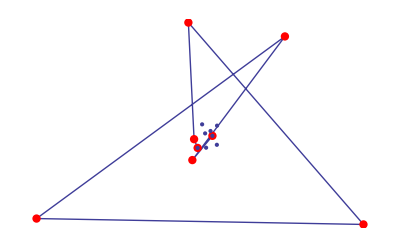

```mathematica
n=7;  (* degree *)
m=7; (* counting from 0 to m *)
ll=1;  (* domain intervals *)
tt1=Table[t,{t,0.0,1.0,1/m}]; (* data point parameter values *)

knot=Join[Table[0,{i,0,n}],Table[i/ll,{i,1,ll-1}],Table[1,{i,0,n}]]//N;

data1=Table[{(2+t)Cos[t]+ 2RandomReal[], (2+t)Sin[t]+ 2RandomReal[]},{t,0,10.0,10/m}]//N;

approx[n,knot,data1,tt1]
```

Next, we let the number of data equal the number of unknown control points. We get spline interpolation.

SetDelayed::write: Tag Graphics in (GraphicsBox[List[List[List[], List[], List[Hue[0.67`, 0.6`, 0.6`], Thickness[Large], LineBox[List[List[0.8`, 1.2000000000000002`], List[0.8086336213955122`, 1.2128582499964404`], List[0.8173594248878522`, 1.2256704089444668`], List[0.835087578163016`, 1.2511564536952775`], List[0.8716500698752786`, 1.3015754506159314`], List[0.9491997939475434`, 1.400201074133369`], List[0.959308328892302`, 1.412321867355186`], List[0.9695090459338888`, 1.424396569528589`], List[0.9901870263075456`, 1.448407700730153`], List[1.0326491722167948`, 1.4958768705523136`], List[1.1219982046830315`, 1.5886028398727634`], List[1.1335816531770355`, 1.599986176319956`], List[1.1452572837678687`, 1.6113234217187355`], List[1.168885091240019`, 1.6338596393710532`], List[1.2172468913462544`, 1.6783789820947206`], List[1.3183952322064654`, 1.7652052972181855`], List[1.3314535942497172`, 1.7758511768907554`], List[1.3446041383897973`, 1.7864509655149117`], List[1.3711817729604405`, 1.8075122696179826`], List[1.4254432272636626`, 1.849081785243157`], List[1.5383908765178465`, 1.9300084461696352`], List[1.554150815677506`, 1.9407482104882419`], List[1.5700190968654317`, 1.9514338037927168`], List[1.602080685326078`, 1.9726424773592683`], List[1.6675039665865528`, 2.0144097723227805`], List[1.8035509464642294`, 2.095344153571438`], List[1.8210443580761335`, 2.1052171816639245`], List[1.8386461117163013`, 2.1150360387422773`], List[1.8741746450814318`, 2.1345112398565846`], List[1.946531816150879`, 2.172811589915611`], List[2.0964465756465014`, 2.2468120813552974`], List[2.115673459710647`, 2.2558183732216612`], List[2.1350086858030592`, 2.2647704940738933`], List[2.174004164072678`, 2.2825122227359587`], List[2.2532952249510974`, 2.3173456278904982`], List[2.417077764064665`, 2.384412229521213`], List[2.438038120581053`, 2.3925517851614546`], List[2.4591068191257084`, 2.400637169787565`], List[2.501569242299813`, 2.416645425997388`], List[2.587794192987204`, 2.448011886247441`], List[2.7654445117187145`, 2.5081445980691823`], List[2.7866311071541126`, 2.5149371360255905`], List[2.8079121611151607`, 2.5216824447191715`], List[2.850757644614218`, 2.5350313743178563`], List[2.9375821139201586`, 2.561162482361313`], List[3.115765061763346`, 2.6111576938325736`], List[3.1384629936091795`, 2.6171945635837637`], List[3.161255383980665`, 2.623184204072128`], List[3.207123540300593`, 2.6350217972603773`], List[3.2999933552482745`, 2.658130232482964`], Skeleton[626]]]]]], List[Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[Method, List[]], Rule[PlotRange, List[List[0.`, 24.998151151716584`], List[0.`, 24.99999066325131`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Scaled[0.02`], Scaled[0.02`]]]]]) is Protected.

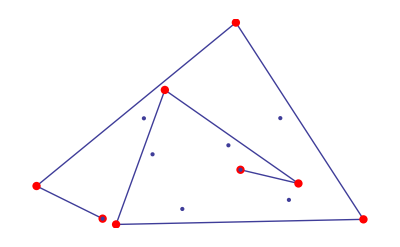

```mathematica
n=3;  (* degree *)
m=7; (* counting from 0 to m *)
ll=5;  (* domain intervals *)
tt1=Table[t,{t,0.0,1.0,1/m}]; (* data point parameter values *)

knot=Join[Table[0,{i,0,n}],Table[i/ll,{i,1,ll-1}],Table[1,{i,0,n}]]//N;

data1=Table[{(2+t)Cos[t]+ 2RandomReal[], (2+t)Sin[t]+ 2RandomReal[]},{t,0,10.0,10/m}]//N;

approx[n,knot,data1,tt1]
```

Next, we use only one interval and degree 1. We get Piecewise Linear Approximation.

SetDelayed::write: Tag Graphics in (GraphicsBox[List[List[List[], List[], List[Hue[0.67`, 0.6`, 0.6`], Thickness[Large], LineBox[List[List[0.8`, 1.2000000000000002`], List[0.8086336213955122`, 1.2128582499964404`], List[0.8173594248878522`, 1.2256704089444668`], List[0.835087578163016`, 1.2511564536952775`], List[0.8716500698752786`, 1.3015754506159314`], List[0.9491997939475434`, 1.400201074133369`], List[0.959308328892302`, 1.412321867355186`], List[0.9695090459338888`, 1.424396569528589`], List[0.9901870263075456`, 1.448407700730153`], List[1.0326491722167948`, 1.4958768705523136`], List[1.1219982046830315`, 1.5886028398727634`], List[1.1335816531770355`, 1.599986176319956`], List[1.1452572837678687`, 1.6113234217187355`], List[1.168885091240019`, 1.6338596393710532`], List[1.2172468913462544`, 1.6783789820947206`], List[1.3183952322064654`, 1.7652052972181855`], List[1.3314535942497172`, 1.7758511768907554`], List[1.3446041383897973`, 1.7864509655149117`], List[1.3711817729604405`, 1.8075122696179826`], List[1.4254432272636626`, 1.849081785243157`], List[1.5383908765178465`, 1.9300084461696352`], List[1.554150815677506`, 1.9407482104882419`], List[1.5700190968654317`, 1.9514338037927168`], List[1.602080685326078`, 1.9726424773592683`], List[1.6675039665865528`, 2.0144097723227805`], List[1.8035509464642294`, 2.095344153571438`], List[1.8210443580761335`, 2.1052171816639245`], List[1.8386461117163013`, 2.1150360387422773`], List[1.8741746450814318`, 2.1345112398565846`], List[1.946531816150879`, 2.172811589915611`], List[2.0964465756465014`, 2.2468120813552974`], List[2.115673459710647`, 2.2558183732216612`], List[2.1350086858030592`, 2.2647704940738933`], List[2.174004164072678`, 2.2825122227359587`], List[2.2532952249510974`, 2.3173456278904982`], List[2.417077764064665`, 2.384412229521213`], List[2.438038120581053`, 2.3925517851614546`], List[2.4591068191257084`, 2.400637169787565`], List[2.501569242299813`, 2.416645425997388`], List[2.587794192987204`, 2.448011886247441`], List[2.7654445117187145`, 2.5081445980691823`], List[2.7866311071541126`, 2.5149371360255905`], List[2.8079121611151607`, 2.5216824447191715`], List[2.850757644614218`, 2.5350313743178563`], List[2.9375821139201586`, 2.561162482361313`], List[3.115765061763346`, 2.6111576938325736`], List[3.1384629936091795`, 2.6171945635837637`], List[3.161255383980665`, 2.623184204072128`], List[3.207123540300593`, 2.6350217972603773`], List[3.2999933552482745`, 2.658130232482964`], Skeleton[626]]]]]], List[Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[Method, List[]], Rule[PlotRange, List[List[0.`, 24.998151151716584`], List[0.`, 24.99999066325131`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Scaled[0.02`], Scaled[0.02`]]]]]) is Protected.

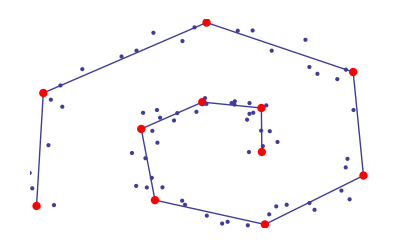

```mathematica
n=1;  (* degree *)
m=70; (* counting from 0 to m *)
ll=10;  (* domain intervals *)
tt1=Table[t,{t,0.0,1.0,1/m}]; (* data point parameter values *)

knot=Join[Table[0,{i,0,n}],Table[i/ll,{i,1,ll-1}],Table[1,{i,0,n}]]//N;

data1=Table[{(2+t)Cos[t]+ 2RandomReal[], (2+t)Sin[t]+ 2RandomReal[]},{t,0,10.0,10/m}]//N;

approx[n,knot,data1,tt1]
```

Next, we use only one interval and degree 1. We get Linear Regression.

SetDelayed::write: Tag Graphics in (GraphicsBox[List[List[List[], List[], List[Hue[0.67`, 0.6`, 0.6`], Thickness[Large], LineBox[List[List[0.8`, 1.2000000000000002`], List[0.8086336213955122`, 1.2128582499964404`], List[0.8173594248878522`, 1.2256704089444668`], List[0.835087578163016`, 1.2511564536952775`], List[0.8716500698752786`, 1.3015754506159314`], List[0.9491997939475434`, 1.400201074133369`], List[0.959308328892302`, 1.412321867355186`], List[0.9695090459338888`, 1.424396569528589`], List[0.9901870263075456`, 1.448407700730153`], List[1.0326491722167948`, 1.4958768705523136`], List[1.1219982046830315`, 1.5886028398727634`], List[1.1335816531770355`, 1.599986176319956`], List[1.1452572837678687`, 1.6113234217187355`], List[1.168885091240019`, 1.6338596393710532`], List[1.2172468913462544`, 1.6783789820947206`], List[1.3183952322064654`, 1.7652052972181855`], List[1.3314535942497172`, 1.7758511768907554`], List[1.3446041383897973`, 1.7864509655149117`], List[1.3711817729604405`, 1.8075122696179826`], List[1.4254432272636626`, 1.849081785243157`], List[1.5383908765178465`, 1.9300084461696352`], List[1.554150815677506`, 1.9407482104882419`], List[1.5700190968654317`, 1.9514338037927168`], List[1.602080685326078`, 1.9726424773592683`], List[1.6675039665865528`, 2.0144097723227805`], List[1.8035509464642294`, 2.095344153571438`], List[1.8210443580761335`, 2.1052171816639245`], List[1.8386461117163013`, 2.1150360387422773`], List[1.8741746450814318`, 2.1345112398565846`], List[1.946531816150879`, 2.172811589915611`], List[2.0964465756465014`, 2.2468120813552974`], List[2.115673459710647`, 2.2558183732216612`], List[2.1350086858030592`, 2.2647704940738933`], List[2.174004164072678`, 2.2825122227359587`], List[2.2532952249510974`, 2.3173456278904982`], List[2.417077764064665`, 2.384412229521213`], List[2.438038120581053`, 2.3925517851614546`], List[2.4591068191257084`, 2.400637169787565`], List[2.501569242299813`, 2.416645425997388`], List[2.587794192987204`, 2.448011886247441`], List[2.7654445117187145`, 2.5081445980691823`], List[2.7866311071541126`, 2.5149371360255905`], List[2.8079121611151607`, 2.5216824447191715`], List[2.850757644614218`, 2.5350313743178563`], List[2.9375821139201586`, 2.561162482361313`], List[3.115765061763346`, 2.6111576938325736`], List[3.1384629936091795`, 2.6171945635837637`], List[3.161255383980665`, 2.623184204072128`], List[3.207123540300593`, 2.6350217972603773`], List[3.2999933552482745`, 2.658130232482964`], Skeleton[626]]]]]], List[Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[Method, List[]], Rule[PlotRange, List[List[0.`, 24.998151151716584`], List[0.`, 24.99999066325131`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Scaled[0.02`], Scaled[0.02`]]]]]) is Protected.

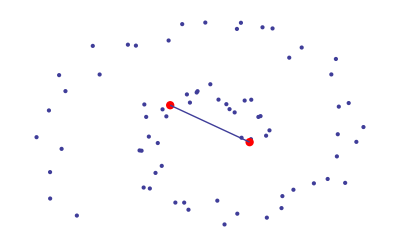

```mathematica
n=1;  (* degree *)
m=70; (* counting from 0 to m *)
ll=1;  (* domain intervals *)
tt1=Table[t,{t,0.0,1.0,1/m}]; (* data point parameter values *)

knot=Join[Table[0,{i,0,n}],Table[i/ll,{i,1,ll-1}],Table[1,{i,0,n}]]//N;

data1=Table[{(2+t)Cos[t]+ 2RandomReal[], (2+t)Sin[t]+ 2RandomReal[]},{t,0,10.0,10/m}]//N;

(* use a different order to display our geometry, simply for better viewing *)
approx1[n_,knot_,data_,tt_]:=
(m=Length[data]-1;
ll=Length[knot]-2*n-1; (* domain intervals *)

(* van is the Vandermonde matrix which typically has (many) more roes than columns *)
van=Table[BSplineBasis[{n,knot},j,tt[[i]]],{i,1,m+1},{j,0,n+ll-1 }];
dd=LinearSolve[Transpose[van].van,Transpose[van].data];
dataplot=ListPlot[data,PlotStyle-> Thick];
points=Graphics[{Red,PointSize[0.015],Point[dd]}];
ddplot=ListLinePlot[dd];
curve[t_]:=Sum[BSplineBasis[{n,knot},i,t]*dd[[i+1]],{i,0,n+ll-1}];
cplot=ParametricPlot[curve[t],{t,knot[[1]],knot[[2n+ll+1]]},PlotStyle->{Thick,Green}];
approxpic=Show[{dataplot,cplot, points,ddplot},Axes-> False]
);
approx1[n,knot,data1,tt1]
```